```mathematica
test[primeList_] :=N[1/(2^(∑_p^primeList 1/(log(p))))]
```

```mathematica
test[{3,5,7}]
```

0.242243

```mathematica
magicX[primeList_] :=N[(∏_p^primeList (1/p+1)^(Log[x+1]/(log(p))))/(2^(∑_p^primeList Log[x+1]/(log(p))))(x)]
```

```mathematica
magicX[{3,5,7}]
```

x/(1.+x)^0.97405

```mathematica
2^(-(1/Log[a]+1/Log[b]+1/Log[c]+1/Log[d]) Log[1+x]) (1+1/a)^(Log[1+x]/Log[a]) (1+1/b)^(Log[1+x]/Log[b]) (1+1/c)^(Log[1+x]/Log[c]) (1+1/d)^(Log[1+x]/Log[d]) x
```

```mathematica
1-0.9740496777265129
```

0.0259503

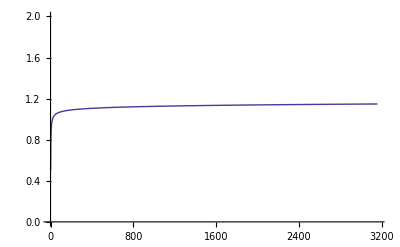

```mathematica
Plot[magicX[{7,11,17,19}],{x,1,3160}, PlotRange->{{0,3160},{0,2}}, GridLines->{Automatic,{{1/E, {Red, Thick}}}}]
```

```mathematica
With[{x=3160}, x/(1.+x)^1.226827941417299]
```

0.160696

```mathematica
N[1/E]
```

0.367879

```mathematica
With[{primelist={3,5,7}},Limit[N[(∏_p^primeList (1/p+1)^(Log[x]/Log[p]))/(2^(∑_p^primeList Log[x]/Log[p]))x], x->Infinity]]
```

Power::infy: Infinite expression 1/0 encountered.

∞::indet: Indeterminate expression 2^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

NSum::nslim: Limit of summation primeList is not a number.

General::stop: Further output of NSum will be suppressed during this calculation.

NProduct::nplim: Limit of product primeList is not a number.

General::stop: Further output of NProduct will be suppressed during this calculation.

Limit[2.^(-1. NSum[Log[x]/Log[p],{p,primeList}]) x NProduct[(1+1/p)^(Log[x]/Log[p]),{p,primeList}],x→∞]

```mathematica
Limit[HarmonicNumber[n,3]HarmonicNumber[n,5]HarmonicNumber[n,7]HarmonicNumber[n,11],n->Infinity]
```

Zeta[3] Zeta[5] Zeta[7] Zeta[11]

```mathematica
magicX2[primeList_] :=N[(∏_p^primeList (1/p+1)^HarmonicNumber[x,p])/1]
```

```mathematica
m
```

```mathematica
Limit[magicX2[{3,5,7}], x->Infinity]
```

Limit[2.^(2. HarmonicNumber[x,3.]+HarmonicNumber[x,5.]+3. HarmonicNumber[x,7.]) 3.^(-1. HarmonicNumber[x,3.]+HarmonicNumber[x,5.]) 5.^(-1. HarmonicNumber[x,5.]) 7.^(-1. HarmonicNumber[x,7.]),x→∞]

```mathematica
N[Zeta[3] Zeta[5] Zeta[7] ]
```

1.25685

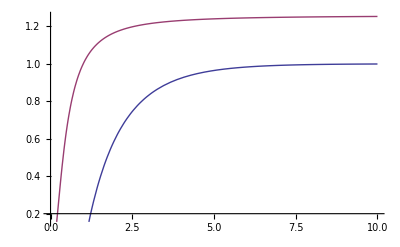

```mathematica
Plot[{1/Zeta[n], HarmonicNumber[n,3]HarmonicNumber[n,5]HarmonicNumber[n,7]HarmonicNumber[n,11]},{n,0,10}]
```

```mathematica
Zeta[3]
```

Zeta[3]

```mathematica
With[{p=11},Limit[(1/p+1)^HarmonicNumber[x,p],x->Infinity]]
```

(12/11)^Zeta[11]

```mathematica
With[{p=5},Limit[(1/p+1)^HarmonicNumber[x,p],x->Infinity]]
```

(6/5)^Zeta[5]

```mathematica
With[{primeList={3,5,7}},Limit[N[(∏_p^primeList (1/p+1)^(Log[x+1]/(log(p))))/(2^(∑_p^primeList Log[x+1]/(log(p))))(x+1)],x->Infinity]]
```

```mathematica
magic[primeList_] :=N[(∏_p^primeList (1/p+1)^(1/(log(p))))/(2^(∑_p^primeList 1/(log(p))))]
```

```mathematica
Convergents[magic[{43,109,131,149,163,179,193}],50]
```

ContinuedFraction::incomp: Warning: ContinuedFraction terminated before 50 terms.

{0,1/2,1/3,3/8,4/11,7/19,32/87,39/106,149/405,337/916,823/2237,1160/3153,8943/24308,45875/124693,421818/1146545,889511/2417783,2200840/5982111}

```mathematica
Convergents[1/E,50]
```

{0,1/2,1/3,3/8,4/11,7/19,32/87,39/106,71/193,465/1264,536/1457,1001/2721,8544/23225,9545/25946,18089/49171,190435/517656,208524/566827,398959/1084483,4996032/13580623,5394991/14665106,10391023/28245729,150869313/410105312,161260336/438351041,312129649/848456353,5155334720/14013652689,5467464369/14862109042,10622799089/28875761731,196677847971/534625820200,207300647060/563501581931,403978495031/1098127402131,8286870547680/22526049624551,8690849042711/23624177026682,16977719590391/46150226651233,382200680031313/1038929163353808,399178399621704/1085079390005041,781379079653017/2124008553358849,19152276311294112/52061284670617417,19933655390947129/54185293223976266,39085931702241241/106246577894593683,1036167879649219395/2816596318483412024,1075253811351460636/2922842896378005707,2111421691000680031/5739439214861417731,60195061159370501504/163627140912497702175,62306482850371181535/169366580127359119906,122501544009741683039/332993721039856822081,3737352803142621672705/10159178211323063782336,3859854347152363355744/10492171932362920604417,7597207150294985028449/20651350143685984386753,246970483156591884266112/671335376530314420980513,254567690306886869294561/691986726674000405367266}

```mathematica
ListPlot[Convergents[magic[{3,5,61,97}],50], GridLines->{Automatic,{{1/E,{Red, Thick}}}}, PlotRange->{All,{0.3675,0.3680}}]
```

```mathematica
Convergents[magic[{17,5417,20441,703357,192272677}],50]
```

ContinuedFraction::incomp: Warning: ContinuedFraction terminated before 50 terms.

{0,1,1/2,2/3,5/8,17/27,328/521,345/548,1363/2165,1708/2713,199491/316873,999163/1587078,1198654/1903951,3396471/5394980,7991596/12693911,11388067/18088891,19379663/30782802}

```mathematica
FactorInteger[691986726674000405367266]
```

{{2,1},{29,1},{193,1},{1543,1},{40063283061092723,1}}

ContinuedFraction::incomp: Warning: ContinuedFraction terminated before 50 terms.

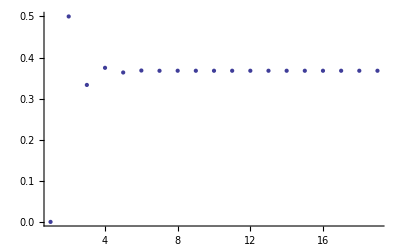

```mathematica
ListPlot[Convergents[magic[{11,31,83,149,179,193}],50], GridLines->{Automatic,{{1/E,{Red, Thick}}}}]
```

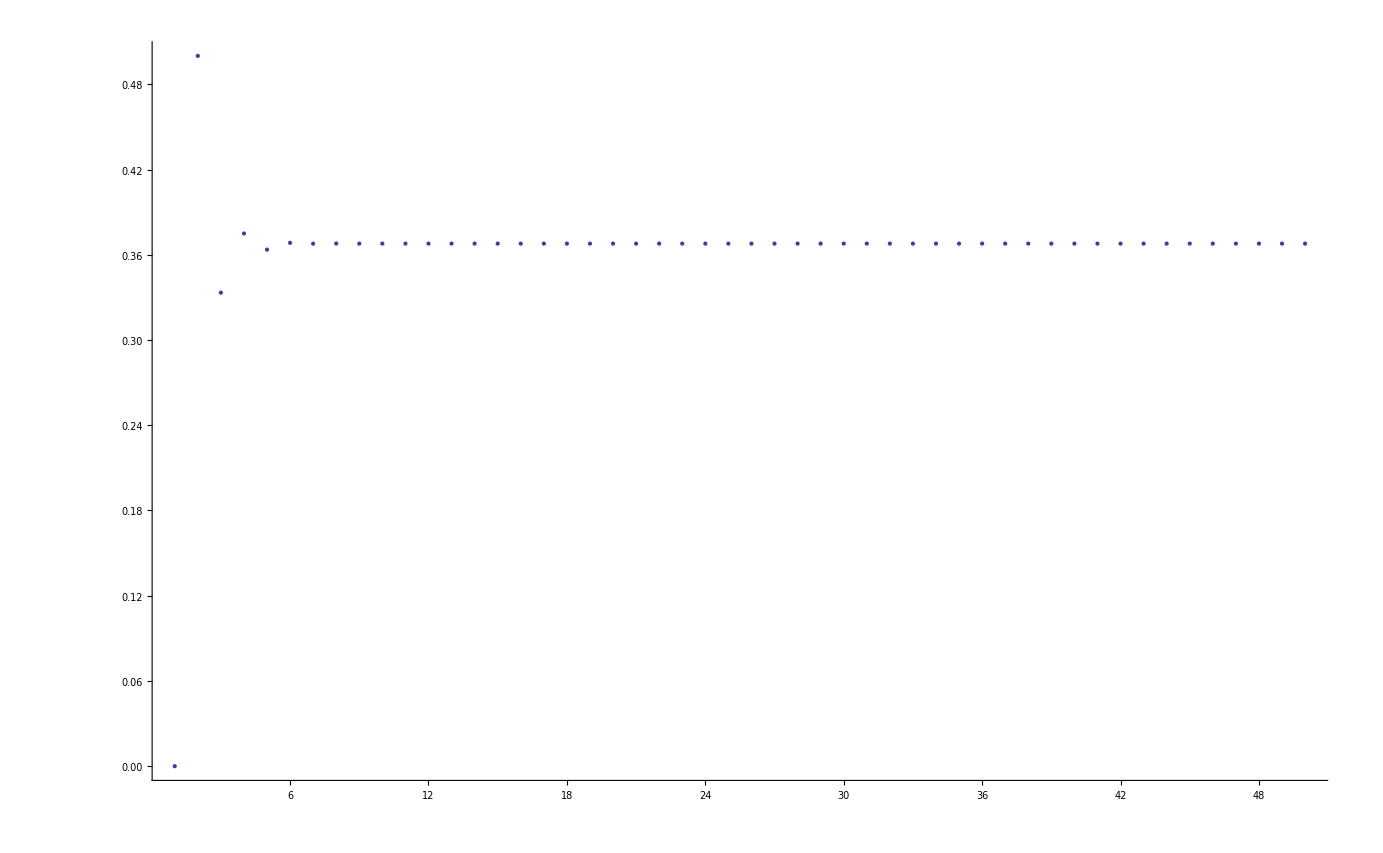

```mathematica
ListPlot[Convergents[1/E,50], GridLines->{Automatic,{{1/E,{Red, Thick}}}}]
```

```mathematica
Inv[PrimeList_]:= Sum[((p+1)/2 )/ (p-1), {p,PrimeList}]
```

```mathematica
N[Inv[{3,5,7}]]
```

2.41667

```mathematica
N[E]
```

2.71828

```mathematica
Inv[{p,q,r}]
```

(1+p)/(2 (-1+p))+(1+q)/(2 (-1+q))+(1+r)/(2 (-1+r))

```mathematica
Limit[(1+1/n)^(n), n->e]
```

(1+1/e)^e

```mathematica
Prime[10]
```

29

```mathematica
Prime[8]
```

19